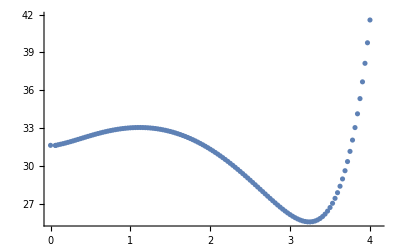

```mathematica
h4={{0,31.631623},{0.062500,31.624624},{0.062500,31.624624},{0.093750,31.675087},{0.125000,31.717935},{0.156250,31.763840},{0.187500,31.813589},{0.218750,31.866713},{0.250000,31.922539},{0.281250,31.980401},{0.312500,32.039692},{0.343750,32.099868},{0.375000,32.160450},{0.406250,32.221008},{0.437500,32.281162},{0.468750,32.340568},{0.500000,32.398919},{0.531250,32.455936},{0.562500,32.511365},{0.593750,32.564975},{0.625000,32.616556},{0.656250,32.665913},{0.687500,32.712869},{0.718750,32.757259},{0.750000,32.798931},{0.781250,32.837746},{0.812500,32.873572},{0.843750,32.906288},{0.875000,32.935783},{0.906250,32.961951},{0.937500,32.984695},{0.968750,33.003922},{1.000000,33.019549},{1.031250,33.031496},{1.062500,33.039687},{1.093750,33.044054},{1.125000,33.044532},{1.156250,33.041059},{1.187500,33.033579},{1.218750,33.022039},{1.250000,33.006390},{1.281250,32.986584},{1.312500,32.962580},{1.343750,32.934338},{1.375000,32.901821},{1.406250,32.864995},{1.437500,32.823830},{1.468750,32.778298},{1.500000,32.728373},{1.531250,32.674034},{1.562500,32.615261},{1.593750,32.552037},{1.625000,32.484350},{1.656250,32.412188},{1.687500,32.335545},{1.718750,32.254417},{1.750000,32.168802},{1.781250,32.078706},{1.812500,31.984134},{1.843750,31.885099},{1.875000,31.781616},{1.906250,31.673707},{1.937500,31.561397},{1.968750,31.444720},{2.000000,31.323712},{2.031250,31.198420},{2.062500,31.068896},{2.093750,30.935201},{2.125000,30.797404},{2.156250,30.655586},{2.187500,30.509837},{2.218750,30.360260},{2.250000,30.206970},{2.281250,30.050098},{2.312500,29.889789},{2.343750,29.726206},{2.375000,29.559534},{2.406250,29.389974},{2.437500,29.217754},{2.468750,29.043127},{2.500000,28.866372},{2.531250,28.687801},{2.562500,28.507757},{2.593750,28.326621},{2.625000,28.144815},{2.656250,27.962803},{2.687500,27.781097},{2.718750,27.600261},{2.750000,27.420916},{2.781250,27.243743},{2.812500,27.069488},{2.843750,26.898972},{2.875000,26.733089},{2.906250,26.572818},{2.937500,26.419227},{2.968750,26.273477},{3.000000,26.136831},{3.031250,26.010662},{3.062500,25.896452},{3.093750,25.795809},{3.125000,25.710463},{3.156250,25.642278},{3.187500,25.593254},{3.218750,25.565534},{3.250000,25.561407},{3.281250,25.583311},{3.312500,25.633834},{3.343750,25.715717},{3.375000,25.831852},{3.406250,25.985281},{3.437500,26.179192},{3.468750,26.416918},{3.500000,26.701935},{3.531250,27.037855},{3.562500,27.428434},{3.593750,27.877576},{3.625000,28.389349},{3.656250,28.968022},{3.687500,29.618112},{3.718750,30.344474},{3.750000,31.152424},{3.781250,32.047925},{3.812500,33.037845},{3.843750,34.130311},{3.875000,35.335188},{3.906250,36.664663},{3.937500,38.133931},{3.968750,39.761664},{4.000000,41.568299},{4.031250,43.566827},{4.062500,45.754563},{4.093750,47.996598}};
ListPlot[h4]
```

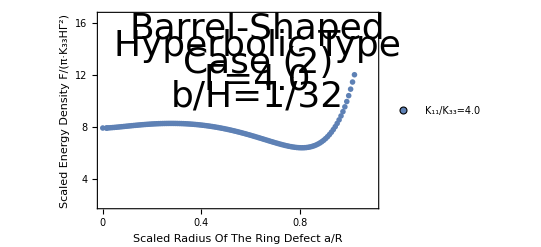

```mathematica
gg4=h4*Table[{0.25,4/16},{i,0,131}];
ListPlot[{gg4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{4,8,12,16},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.1},{2,16.5}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.63,15.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.63,14.2}],Text[Style["Case (2)",Directive[Black,36]],{0.63,12.9}],Text[Style["Γ=4.0",Directive[Black,36]],{0.63,11.6}],Text[Style["b/H=1/32",Directive[Black,36]],{0.63,10.3}]}]
```